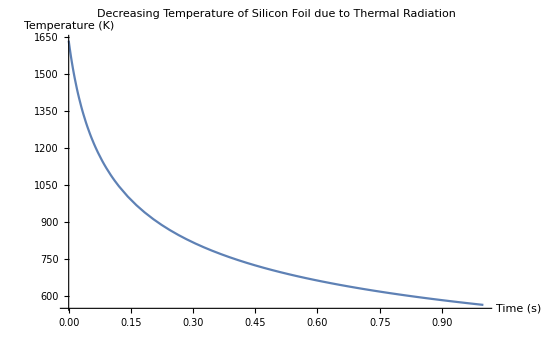

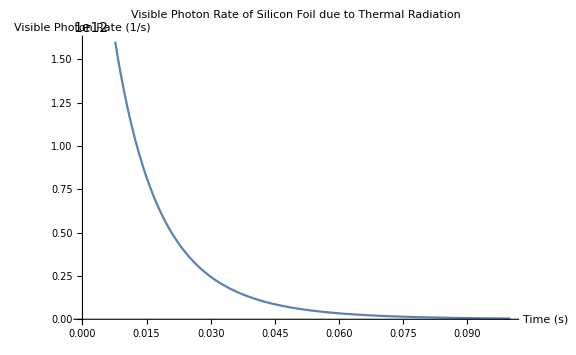

NIntegrate::inumr: The integrand 1.19104×10^-16/(-1 + ⅇ^8.79986×10^-6\ (1 + Times[« 2 »])^1/3/lambda)\ lambda^5 has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

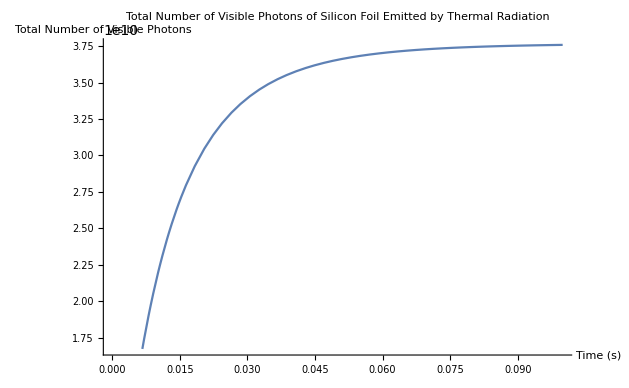

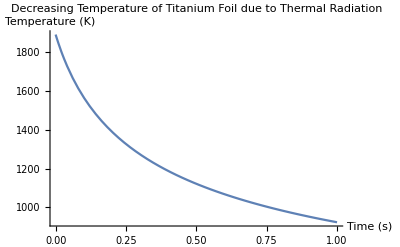

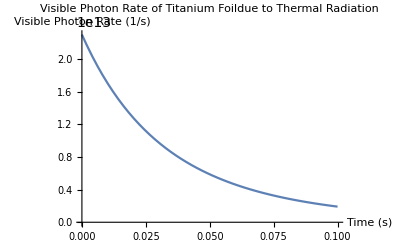

NIntegrate::inumr: The integrand 1.19104×10^-16/(-1 + ⅇ^7.60855×10^-6\ (1 + Times[« 2 »])^1/3/lambda)\ lambda^5 has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

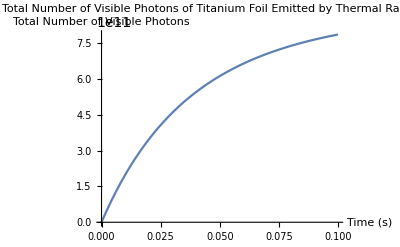

```mathematica
c=299792458;
hbar=1.05457173*^-34;
h=hbar*2*Pi;
e=1.602*^-19;
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;
kB=1.3806488*^-23;
delta=25*^-6;
sig=2*Pi^5/15*kB^4/(c^2*h^3);

(*Silicon Material Properties*)
rho=2330;
cp=710 (*0.00071*);
Tmelt=1412+273;
Th=Tmelt-50;
emmis=0.65;

Temp[t_]:=
Th*(1+6*sig*emmis*Th^3/(delta*rho*cp)*t)^(-1/3)

blackbody[lambda_,t_]:=
2*h*c^2/lambda^5*1/(Exp[h*c/(lambda*kB*Temp[t])]-1)

dndt[t_]:=
NIntegrate[blackbody[lambda,t],{lambda,lowerlambda,upperlambda}]*2*Pi*Pi*sigy^2*averagelambda/(h*c)

nphotons[t_]:=
NIntegrate[dndt[t0],{t0,0,t}]

Plot[Temp[t],{t,0,1},AxesLabel-> {"Time (s)","Temperature (K)"},PlotLabel->Style["Decreasing Temperature of Silicon Foil due to Thermal Radiation",FontSize->18]]

Plot[dndt[t],{t,0,0.1},AxesLabel-> {"Time (s)","Visible Photon Rate (1/s)"},PlotLabel->Style["Visible Photon Rate of Silicon Foil due to Thermal Radiation",FontSize->18]]

Plot[nphotons[t],{t,0,0.1},AxesLabel-> {"Time (s)","Total Number of Visible Photons"},PlotLabel->Style["Total Number of Visible Photons of Silicon Foil Emitted by Thermal Radiation",FontSize->18]]


(*Titanium Material Properties*)
rho=4500;
cp=540;
Tmelt=1668+273;
Th=Tmelt-50;
emmis=0.2;


Plot[Temp[t],{t,0,1},AxesLabel-> {"Time (s)","Temperature (K)"},PlotLabel->Style["Decreasing Temperature of Titanium Foil due to Thermal Radiation",FontSize->18]]

Plot[dndt[t],{t,0,0.1},AxesLabel-> {"Time (s)","Visible Photon Rate (1/s)"},PlotLabel->Style["Visible Photon Rate of Titanium Foildue to Thermal Radiation",FontSize->18]]

Plot[nphotons[t],{t,0,0.1},AxesLabel-> {"Time (s)","Total Number of Visible Photons"},PlotLabel->Style["Total Number of Visible Photons of Titanium Foil Emitted by Thermal Radiation",FontSize->18]]
```

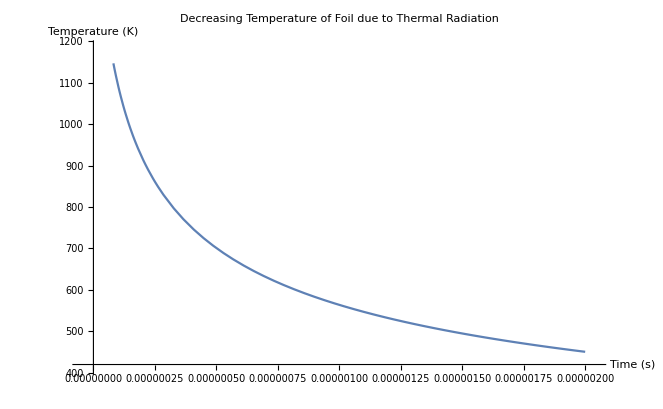

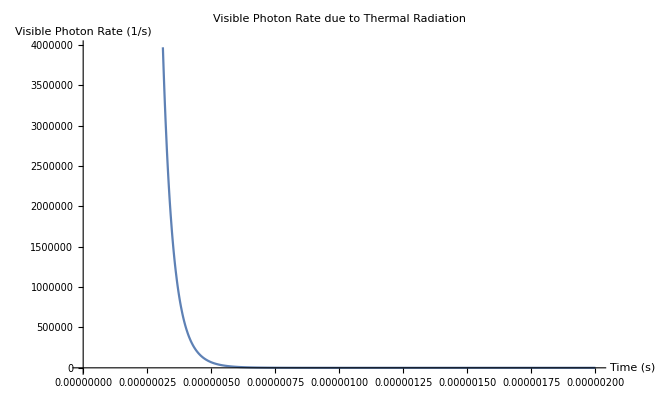

NIntegrate::inumr: The integrand 1.19104×10^-16/(-1 + ⅇ^8.79986×10^-6\ (1 + Times[« 2 »])^1/3/lambda)\ lambda^5 has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.